zad 2

```mathematica
p=0;
q=6;
```

```mathematica
(*lokalicaciq na koren chrez metoda na xordite*)
```

```mathematica
f[x_] :=x^3 -(p+40)Sin[x]-3(q+p+1);
```

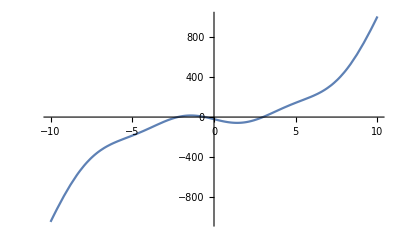

```mathematica
Plot[f[x],{x,-10,10}]
```

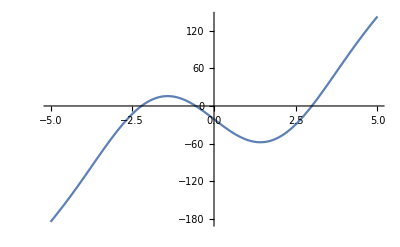

```mathematica
Plot[f[x],{x,-5,5},AxesOrigin->{0,0}]
```

```mathematica
(*broq na korenite e 3*)
```

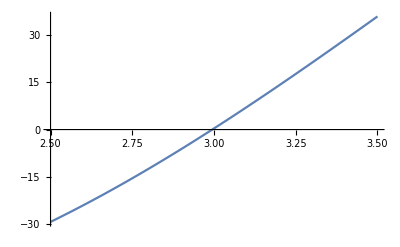

```mathematica
Plot[f[x],{x,2.5,3.5}]
```

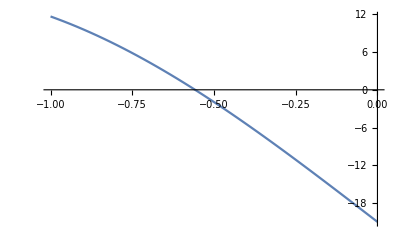

```mathematica
Plot[f[x],{x,-1,0}]
```

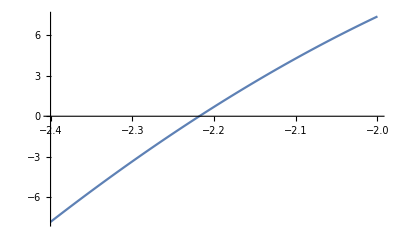

```mathematica
(*lokalizirame nai-malkiq koren*)
Plot[f[x],{x,-2.4,-2}]
```

```mathematica
a=-2.4;b=-2;
```

```mathematica
f[N[a]]
```

-7.80547

```mathematica
f[N[b]]
```

7.3719

имаме корен, защото знакът се променя в дадения интервал

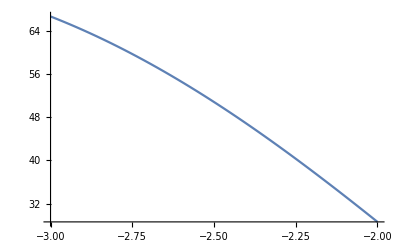

```mathematica
(*proverqvame usloviqta na metoda=>dali f' i f'' sa s postoqnen znak*)
Plot[f'[x],{x,a,b}]
```

izvod: purvata proizvodna e s postoqnen znak (v opredeleniq interval) f’(x)>0

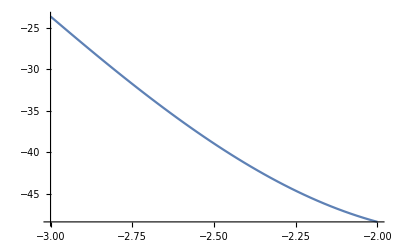

```mathematica
Plot[f''[x],{x,a,b}]
```

izvod : vtorata proizvodna e s postoqnen znak (v opredeleniq interval) f'' (x) < 0

izbirame nachalno priblijenie f(x0).f’’<0   pri f’’<0   x0 trqbva da e >0
izbirame -2 za postoqnna tochka

```mathematica
x0=-2.; (*nachalno priblijenie*)
p = -2.4; (*postoqnna tochka*)

f[x0]
```

12.3896

```mathematica
f[p]
```

-2.22658

```mathematica
m1=Abs[f'[-2.]](*minimum*)
```

27.6471

```mathematica
M1=Abs[f'[-2.4]]
```

45.006

```mathematica
K=(M1 - m1)/m1
```

0.627873

```mathematica
xprev=x0; (*predishna tochka*)
Print["n=0"," x=",x0," f[x]",f[x0]];
For[n=0,n<5,n++,
xnext=xprev - f[xprev]/(f[xprev]-f[p])(xprev-5); (*sledvashtata tochka*)
eps = K*Abs[xnext-xprev]; (*tekushta greshka*)

Print["n=", n+1," x= ",xnext," f[x] ",SetPrecision[f[xnext],14]," eps ", eps];
xprev = xnext;
]
```

n=0 x=-2. f[x]12.3896

n=1 x= 3.93364 f[x] 73.830709004579 eps 3.72557

n=2 x= 4.96878 f[x] 145.24414499176 eps 0.649938

n=3 x= 4.99953 f[x] 147.22522865305 eps 0.0193049

n=4 x= 4.99999 f[x] 147.25510095874 eps 0.000291533

n=5 x= 5. f[x] 147.25554599808 eps 4.34338×10^-6